```mathematica
(*This first part is what you already know*)
```

```mathematica
Clear[kt,u, d,g,rs, a, b,Ks,x, rho1,rho2,rho3, rhodash, rhodash1, rhodash2,rhodash3, lgs, lgs1,lgs2, lgs3,lgs4,lgs5,lgs6,k,fk,kulim0,kliminf,dk]
```

```mathematica
kt = 1;
rs = 1;
```

```mathematica
(*Transition matrix for Barrier*)
```

```mathematica
w = {{-g,g},{g,-g}};
```

```mathematica
(*evec = Eigenvectors[w] Use hard coded definition instead to assure correct order of eigenvalues *)
```

```mathematica
evec = {{1,1},{-1,1}}
```

{{1,1},{-1,1}}

```mathematica
s = Transpose[{Normalize[evec[[1]]],Normalize[evec[[2]]]}]
```

{{1/(√2),-1/(√2)},{1/(√2),1/(√2)}}

```mathematica
invs = Simplify[Assuming[{ab>0, ba>0},Inverse[s]]]
```

{{1/(√2),1/(√2)},{-1/(√2),1/(√2)}}

```mathematica
diagw = Simplify[invs.w.s]
```

{{0,0},{0,-2 g}}

```mathematica
(*Assembly of matching matrix*)
```

```mathematica
bcu = {{1,0},{0,Exp[u/kt]}}
```

{{1,0},{0,ⅇ^u}}

```mathematica
(*Do handy substitutions first before things get out of hand!*)
```

```mathematica
rhodash[r_] = {{1, 1/r, 0, 0},{0, 0, Exp[-Sqrt[Abs[diagw[[2,2]]]/d]r]/r,Exp[Sqrt[Abs[diagw[[2,2]]]/d]r]/r}} /.√2 √(1/d) √Abs[g]->x
```

{{1,1/r,0,0},{0,0,ⅇ^(-r x)/r,ⅇ^(r x)/r}}

```mathematica
(*Build system of linear equations for fitting and boundary conditions*)
```

```mathematica
lgs1 = Join[rhodash'[rs]-Ks rhodash[rs],{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}},2];
lgs2 = Join[rhodash[a], -invs.bcu.s.rhodash[a], {{0,0,0,0},{0,0,0,0}},2];
lgs3 = Join[rhodash'[a],-rhodash'[a],{{0,0,0,0},{0,0,0,0}},2];
lgs4= Join[{{0,0,0,0},{0,0,0,0}},invs.bcu.s.rhodash[b],-rhodash[b],2];
lgs5 = Join[{{0,0,0,0},{0,0,0,0}},rhodash'[b],-rhodash'[b],2];
lgs6 = Join[{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}},{{1,0,0,0},{0,0,0,Infinity}},2];
```

```mathematica
lgs = Join[lgs1, lgs2, lgs3, lgs4,lgs5,lgs6,1];
```

```mathematica
lgs = lgs[[1;;11,1;;11]];
```

```mathematica
(*Calculation of matching constants*)
```

```mathematica
c =Assuming[{g>0,d>0,kt>0,b>a>rs>0}, LinearSolve[lgs,Transpose[{{0,0,0,0,0,0,0,0,0,0,1}}]]];
```

```mathematica
c = Assuming[b > a > rs > 0,Simplify[c]];
```

```mathematica
c = Join[c,{{0}}];
```

```mathematica
(*Check, if matching worked out*)
```

```mathematica
(*Simplify[lgs.c[[1;;11]]]*)
```

```mathematica
rhodash1[r_] = rhodash[r].c[[1;;4]];
```

```mathematica
(*Simplify[rhodash1[rs]]*)
```

```mathematica
rhodash2[r_] = rhodash[r].c[[5;;8]];
```

```mathematica
rhodash3[r_] = rhodash[r].c[[9;;12]];
```

```mathematica
(*Simplify[invs.bcu.s.rhodash2[b] - rhodash3[b]]
Simplify[rhodash2'[b] - rhodash3'[b]]
Simplify[rhodash3[Infinity]]*)
```

```mathematica
(*Calculatio normalization of density profiles*)
```

```mathematica
n = Limit[Total[Total[s.rhodash3[r]]],r->Infinity]
```

√2

```mathematica
(*Calculate density profiles*)
```

```mathematica
rho1[r_] = s.rhodash1[r]/n;
rho2[r_] = s.rhodash2[r]/n;
rho3[r_] = s.rhodash3[r]/n;
```

```mathematica
rhom1[r_] =Part[rho1[r],1]+ Part[rho1[r],2];
rhom2[r_] =Part[rho2[r],1]+ Part[rho2[r],2];
rhom3[r_] =Part[rho3[r],1]+ Part[rho3[r],2];
```

```mathematica
(*Calculate absorption rate (omit the 4 pi D Rs) such that the result is normalized to the debye result for the ungated problem*)
```

```mathematica
rho1dash[r_] := rhom1'[r]
```

```mathematica
k =  Simplify[Total[rho1dash[1]]]
```

-(Ks (2 ⅇ^(u+2 (1+b) x) (-1-Ks+x) (1+a x) (-1+b x)+2 b ⅇ^((2+a+b) x) x (-1-Ks+x) (1+b x)-4 b ⅇ^(u+(2+a+b) x) x (-1-Ks+x) (1+b x)+2 b ⅇ^(2 u+(2+a+b) x) x (-1-Ks+x) (1+b x)+2 b ⅇ^((3 a+b) x) x (1+Ks+x) (1+b x)-4 b ⅇ^(u+3 a x+b x) x (1+Ks+x) (1+b x)+2 b ⅇ^(2 u+3 a x+b x) x (1+Ks+x) (1+b x)+ⅇ^(2 (1+a) x) (-1-Ks+x) (-1+a x) (1+b x)+ⅇ^(4 a x) (1+Ks+x) (-1+a x) (1+b x)-2 ⅇ^(u+4 a x) (1+Ks+x) (-1+a x) (1+b x)+ⅇ^(2 u+4 a x) (1+Ks+x) (-1+a x) (1+b x)+2 ⅇ^(u+2 (1+a) x) (-1-Ks+x) (1+a x) (1+b x)+ⅇ^(2 (u+x+b x)) (-1-Ks+x) (1+a x) (1+b x)-ⅇ^(2 (u+(a+b) x)) (1+Ks+x) (-1+3 a x) (1+b x)-ⅇ^(2 (u+x+a x)) (-1-Ks+x) (1+3 a x) (1+b x)-ⅇ^(2 (1+b) x) (-1-Ks+x) (1+a x) (-1+3 b x)-ⅇ^(2 (a+b) x) (1+Ks+x) (1+a x) (-1+3 b x)-2 ⅇ^(u+2 (a+b) x) (1+Ks+x) (1-b x+a x (-1+5 b x))))/(-ⅇ^(4 a x) (1+Ks) (1+Ks+x) (-1+a x) (1+b x)+2 ⅇ^(u+4 a x) (1+Ks) (1+Ks+x) (-1+a x) (1+b x)-ⅇ^(2 u+4 a x) (1+Ks) (1+Ks+x) (-1+a x) (1+b x)-ⅇ^(2 (u+x+b x)) (-1-Ks+x) (1+a x) (1+Ks+3 b x-2 Ks x+3 b Ks x)+2 ⅇ^(u+2 (1+a) x) (-1-Ks+x) (1+b x) (-1+a x+Ks (-1+(-2+a) x))+ⅇ^(2 (u+x+a x)) (-1-Ks+x) (1+b x) (1+a x+Ks (1+(2+a) x))-ⅇ^(2 (1+a) x) (-1-Ks+x) (1+b x) (-1+3 a x+Ks (-1+(-2+3 a) x))+2 ⅇ^(u+2 (1+b) x) (-1-Ks+x) (1+a x) (1+b x+Ks (1+(-2+b) x))+ⅇ^(2 (1+b) x) (-1-Ks+x) (1+a x) (-1+b x+Ks (-1+(2+b) x))+2 ⅇ^((2+a+b) x) x (-1-Ks+x) (a^2 (1+Ks) x-Ks (2+b x)+a (1+Ks-Ks x))-4 ⅇ^(u+(2+a+b) x) x (-1-Ks+x) (a^2 (1+Ks) x-Ks (2+b x)+a (1+Ks-Ks x))+2 ⅇ^(2 u+(2+a+b) x) x (-1-Ks+x) (a^2 (1+Ks) x-Ks (2+b x)+a (1+Ks-Ks x))-2 ⅇ^((3 a+b) x) x (1+Ks+x) (a^2 (1+Ks) x+Ks (2+b x)-a (1+Ks+Ks x))+4 ⅇ^(u+3 a x+b x) x (1+Ks+x) (a^2 (1+Ks) x+Ks (2+b x)-a (1+Ks+Ks x))-2 ⅇ^(2 u+3 a x+b x) x (1+Ks+x) (a^2 (1+Ks) x+Ks (2+b x)-a (1+Ks+Ks x))+ⅇ^(2 (u+(a+b) x)) (1+Ks+x) ((-1+a x) (1+3 b x)+Ks (-1+(4+a-3 b) x+3 (a (-2+b)+2 b) x^2))+ⅇ^(2 (a+b) x) (1+Ks+x) ((1+3 a x) (-1+b x)+Ks (-1+(4-3 a+b) x+(2 a-2 b+3 a b) x^2))+2 ⅇ^(u+2 (a+b) x) (1+Ks+x) (1+b x+a x (1+5 b x)+Ks (1+(-4+a+b) x+(2 a-2 b+5 a b) x^2)))

```mathematica
fk[u_,a_,b_,Ks_,x_]:=-(Ks (2 ⅇ^(u+2 (1+b) x) (-1-Ks+x) (1+a x) (-1+b x)+2 b ⅇ^((2+a+b) x) x (-1-Ks+x) (1+b x)-4 b ⅇ^(u+(2+a+b) x) x (-1-Ks+x) (1+b x)+2 b ⅇ^(2 u+(2+a+b) x) x (-1-Ks+x) (1+b x)+2 b ⅇ^((3 a+b) x) x (1+Ks+x) (1+b x)-4 b ⅇ^(u+3 a x+b x) x (1+Ks+x) (1+b x)+2 b ⅇ^(2 u+3 a x+b x) x (1+Ks+x) (1+b x)+ⅇ^(2 (1+a) x) (-1-Ks+x) (-1+a x) (1+b x)+ⅇ^(4 a x) (1+Ks+x) (-1+a x) (1+b x)-2 ⅇ^(u+4 a x) (1+Ks+x) (-1+a x) (1+b x)+ⅇ^(2 u+4 a x) (1+Ks+x) (-1+a x) (1+b x)+2 ⅇ^(u+2 (1+a) x) (-1-Ks+x) (1+a x) (1+b x)+ⅇ^(2 (u+x+b x)) (-1-Ks+x) (1+a x) (1+b x)-ⅇ^(2 (u+(a+b) x)) (1+Ks+x) (-1+3 a x) (1+b x)-ⅇ^(2 (u+x+a x)) (-1-Ks+x) (1+3 a x) (1+b x)-ⅇ^(2 (1+b) x) (-1-Ks+x) (1+a x) (-1+3 b x)-ⅇ^(2 (a+b) x) (1+Ks+x) (1+a x) (-1+3 b x)-2 ⅇ^(u+2 (a+b) x) (1+Ks+x) (1-b x+a x (-1+5 b x))))/(-ⅇ^(4 a x) (1+Ks) (1+Ks+x) (-1+a x) (1+b x)+2 ⅇ^(u+4 a x) (1+Ks) (1+Ks+x) (-1+a x) (1+b x)-ⅇ^(2 u+4 a x) (1+Ks) (1+Ks+x) (-1+a x) (1+b x)-ⅇ^(2 (u+x+b x)) (-1-Ks+x) (1+a x) (1+Ks+3 b x-2 Ks x+3 b Ks x)+2 ⅇ^(u+2 (1+a) x) (-1-Ks+x) (1+b x) (-1+a x+Ks (-1+(-2+a) x))+ⅇ^(2 (u+x+a x)) (-1-Ks+x) (1+b x) (1+a x+Ks (1+(2+a) x))-ⅇ^(2 (1+a) x) (-1-Ks+x) (1+b x) (-1+3 a x+Ks (-1+(-2+3 a) x))+2 ⅇ^(u+2 (1+b) x) (-1-Ks+x) (1+a x) (1+b x+Ks (1+(-2+b) x))+ⅇ^(2 (1+b) x) (-1-Ks+x) (1+a x) (-1+b x+Ks (-1+(2+b) x))+2 ⅇ^((2+a+b) x) x (-1-Ks+x) (a^2 (1+Ks) x-Ks (2+b x)+a (1+Ks-Ks x))-4 ⅇ^(u+(2+a+b) x) x (-1-Ks+x) (a^2 (1+Ks) x-Ks (2+b x)+a (1+Ks-Ks x))+2 ⅇ^(2 u+(2+a+b) x) x (-1-Ks+x) (a^2 (1+Ks) x-Ks (2+b x)+a (1+Ks-Ks x))-2 ⅇ^((3 a+b) x) x (1+Ks+x) (a^2 (1+Ks) x+Ks (2+b x)-a (1+Ks+Ks x))+4 ⅇ^(u+3 a x+b x) x (1+Ks+x) (a^2 (1+Ks) x+Ks (2+b x)-a (1+Ks+Ks x))-2 ⅇ^(2 u+3 a x+b x) x (1+Ks+x) (a^2 (1+Ks) x+Ks (2+b x)-a (1+Ks+Ks x))+ⅇ^(2 (u+(a+b) x)) (1+Ks+x) ((-1+a x) (1+3 b x)+Ks (-1+(4+a-3 b) x+3 (a (-2+b)+2 b) x^2))+ⅇ^(2 (a+b) x) (1+Ks+x) ((1+3 a x) (-1+b x)+Ks (-1+(4-3 a+b) x+(2 a-2 b+3 a b) x^2))+2 ⅇ^(u+2 (a+b) x) (1+Ks+x) (1+b x+a x (1+5 b x)+Ks (1+(-4+a+b) x+(2 a-2 b+5 a b) x^2)))
```

```mathematica
(*Make absorption rate a function of its parameters*)
```

```mathematica
fkeff[u_,a_,b_,Ks_,x_]:=(Ks rs (2 ⅇ^(u+2 (b+rs) x) (1+a x) (-1+b x)-2 b ⅇ^((3 a+b) x) x (1+b x)+2 b ⅇ^((a+b+2 rs) x) x (1+b x)+4 b ⅇ^(u+(3 a+b) x) x (1+b x)-2 b ⅇ^(2 u+(3 a+b) x) x (1+b x)-4 b ⅇ^(u+(a+b+2 rs) x) x (1+b x)+2 b ⅇ^(2 u+(a+b+2 rs) x) x (1+b x)-ⅇ^(4 a x) (-1+a x) (1+b x)+ⅇ^(2 (a+rs) x) (-1+a x) (1+b x)+2 ⅇ^(u+4 a x) (-1+a x) (1+b x)-ⅇ^(2 u+4 a x) (-1+a x) (1+b x)+2 ⅇ^(u+2 (a+rs) x) (1+a x) (1+b x)+ⅇ^(2 (u+(b+rs) x)) (1+a x) (1+b x)+ⅇ^(2 (u+(a+b) x)) (-1+3 a x) (1+b x)-ⅇ^(2 (u+(a+rs) x)) (1+3 a x) (1+b x)+ⅇ^(2 (a+b) x) (1+a x) (-1+3 b x)-ⅇ^(2 (b+rs) x) (1+a x) (-1+3 b x)+2 ⅇ^(u+2 (a+b) x) (1-b x+a x (-1+5 b x))))/(-ⅇ^(4 a x) (Ks+rs) (-1+a x) (1+b x)+2 ⅇ^(u+4 a x) (Ks+rs) (-1+a x) (1+b x)-ⅇ^(2 u+4 a x) (Ks+rs) (-1+a x) (1+b x)+ⅇ^(2 (u+(b+rs) x)) (1+a x) (Ks+rs+3 b Ks x+b rs x-2 Ks rs x)+2 ⅇ^(u+2 (a+rs) x) (1+b x) (Ks+rs-a Ks x+a rs x+2 Ks rs x)-ⅇ^(2 (u+(a+rs) x)) (1+b x) (Ks+rs+a Ks x+3 a rs x+2 Ks rs x)+ⅇ^(2 (a+rs) x) (1+b x) (rs (-1+a x)+Ks (-1+3 a x-2 rs x))+2 ⅇ^(u+2 (b+rs) x) (1+a x) (rs (-1+b x)-Ks (1+b x-2 rs x))+2 ⅇ^((a+b+2 rs) x) x (-a^2 Ks x+rs (b+2 Ks+b^2 x+b Ks x)+a Ks (-1+rs x))-4 ⅇ^(u+(a+b+2 rs) x) x (-a^2 Ks x+rs (b+2 Ks+b^2 x+b Ks x)+a Ks (-1+rs x))+2 ⅇ^(2 u+(a+b+2 rs) x) x (-a^2 Ks x+rs (b+2 Ks+b^2 x+b Ks x)+a Ks (-1+rs x))-ⅇ^(2 (b+rs) x) (1+a x) (rs (-1+3 b x)+Ks (-1+b x+2 rs x))-2 ⅇ^((3 a+b) x) x (a^2 Ks x+rs (b+2 Ks+b^2 x+b Ks x)-a (Ks+Ks rs x))+4 ⅇ^(u+(3 a+b) x) x (a^2 Ks x+rs (b+2 Ks+b^2 x+b Ks x)-a (Ks+Ks rs x))-2 ⅇ^(2 u+(3 a+b) x) x (a^2 Ks x+rs (b+2 Ks+b^2 x+b Ks x)-a (Ks+Ks rs x))+ⅇ^(2 (u+(a+b) x)) (rs (-1+3 a x) (1+b x)+Ks (-1+4 rs x+a x (1+3 b x-6 rs x)+3 b x (-1+2 rs x)))+ⅇ^(2 (a+b) x) (rs (1+a x) (-1+3 b x)+Ks (-1+b x+4 rs x-2 b rs x^2+a x (-3+3 b x+2 rs x)))+2 ⅇ^(u+2 (a+b) x) (rs (1-b x+a x (-1+5 b x))+Ks (1+b x-4 rs x-2 b rs x^2+a x (1+5 b x+2 rs x))))
```

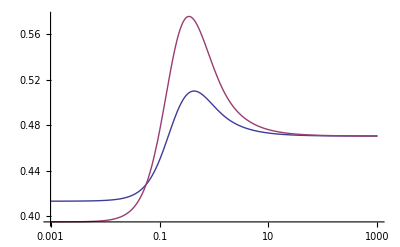

```mathematica
a=6;
b=11;
u=3;
Ks=1;
LogLinearPlot[{fkeff[u,a,b,Ks,x],fk[u,a,b,Ks,x]},{x,10^-3,10^3},PlotRange->All]
ClearAll[a,b,u,Ks]
```

```mathematica
Ksvalues = {0.1, 1, 10}
resolution = 100

tab1 = Table[0, {k, 1, 4}, {i, 1, resolution + 1}, {l, 1, 2}];
tab2 = Table[0, {k, 1, 4}, {i, 1, resolution + 1}, {l, 1, 2}];

For[i = 1, i <= 3, i++,
 g = 1;
 t = 5;
Ks =Ksvalues[[i]];
 a = 1 + t;
 b = 1 + (g + 1) t;
 u = -3;
 dr = 0.02;
 rmin = -3;
 rmax = 3;
 tab1[[i, All, All]] = 
  Table[N[{10^r, fk[u,a, b, Ks, 10^-r]}], {r, rmin, 
    rmax, (rmax - rmin)/resolution}];
 tab2[[i, All, All]] = 
  Table[N[{10^r, fkeff[u,a, b, Ks, 10^-r]}], {r, rmin, 
    rmax, (rmax - rmin)/resolution}];
  ]
Clear[a, b, u,Ks, dr, rmin, rmax, r1, r2, g, t];
For[i = 1, i <= 3, i++,
 Ks = Ksvalues[[i]];
 nfile1 = "attanalytics" <> ToString[Ks] <> ".tsv";
 nfile2 = "attasumption" <> ToString[Ks] <> ".tsv";
 Export[nfile1, tab1[[i, All, All]], "TSV"];
 Export[nfile2, tab2[[i, All, All]], "TSV"];
 ]

tab1 = Table[0, {k, 1, 4}, {i, 1, resolution + 1}, {l, 1, 2}];
tab2 = Table[0, {k, 1, 4}, {i, 1, resolution + 1}, {l, 1, 2}];
tab3 = Table[0, {k, 1, 4}, {i, 1, resolution + 1}, {l, 1, 2}];

For[i = 1, i <= 3, i++,
 g = 1;
 t = 5;
Ks =Ksvalues[[i]];
 a = 1 + t;
 b = 1 + (g + 1) t;
 u = 3;
 dr = 0.02;
 rmin = -3;
 rmax = 3;
 tab1[[i, All, All]] = 
  Table[N[{10^r, fk[u,a, b, Ks, 10^-r]}], {r, rmin, 
    rmax, (rmax - rmin)/resolution}];
 tab2[[i, All, All]] = 
  Table[N[{10^r, fkeff[u,a, b, Ks, 10^-r]}], {r, rmin, 
    rmax, (rmax - rmin)/resolution}];
  ]
Clear[a, b, u,Ks, dr, rmin, rmax, r1, r2, g, t];
For[i = 1, i <= 3, i++,
 Ks = Ksvalues[[i]];
 nfile1 = "repanalytics" <> ToString[Ks] <> ".tsv";
 nfile2 = "repasumption" <> ToString[Ks] <> ".tsv";
 Export[nfile1, tab1[[i, All, All]], "TSV"];
 Export[nfile2, tab2[[i, All, All]], "TSV"];
 ]
```

{0.1,1,10}

100